{{8.22×10^14,1.864},{7.41×10^14,1.416},{6.88×10^14,1.184},{5.49×10^14,0.635},{5.2×10^14,0.513}}

ListPlot::prng: Value of option PlotRange -> {{900000000000000},{0,2.}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

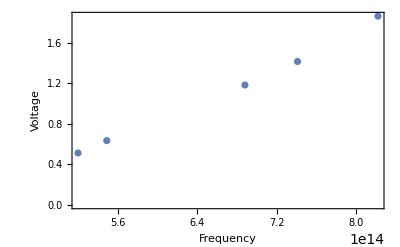

```mathematica
data1 = {{ 8.22*10^(14),1.864},{7.41*10^(14),1.416},{6.88*10^(14),1.184},{5.49*10^(14),0.635},{5.20*10^(14),0.513}}

ListPlot[data1, PlotRange ->{{ 9*10^(14)},{0,2.0}}, Frame -> True, FrameLabel -> {"Frequency", "Voltage"}]
```

ListPlot::prng: Value of option PlotRange -> {{900000000000000},{0,2.}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

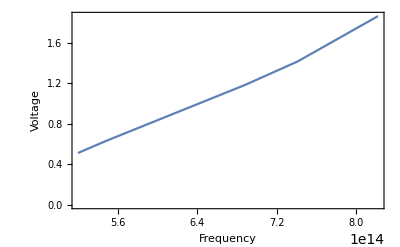

```mathematica
ListPlot[data1, PlotRange ->{{ 9*10^(14)},{0,2.0}}, Frame -> True, FrameLabel -> { "Frequency","Voltage"}, Joined -> True]
```

```mathematica
Fit[data1,{1,x},x]
```

-1.77049+4.35676×10^-15 x

```mathematica
Hcalculate = {4.35676*10^(-15)*1.602*10^(-19)}
```

{6.97953×10^-34}

```mathematica
PercentError = abs[(((6.979*10^(-34))-(6.626*10^(-34)))/(6.626*10^(-34)))*100]
```

abs[5.3275]

ListPlot::prng: Value of option PlotRange -> {{-2.,0},{900000000000000}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.